```mathematica
Clear[kt,koff,kon,nkp]
```

```mathematica
(*FPT of straight path time, no chance of dissociation*)
ptb[x_]=PDF[ErlangDistribution[nkp,kt],x];

(* FPT of dissociation given no chance of activation *)
ptoff[x_]=PDF[ExponentialDistribution[koff],x];
```

```mathematica
(* Working out distributions *)
```

```mathematica
(*tST remains constant*)
```

```mathematica
ftST[ts_]=PDF[ErlangDistribution[nkp,koff+kt],ts]
```

Piecewise[{{(ⅇ^(-((koff+kt) ts)) (koff+kt)^nkp ts^(-1+nkp))/Gamma[nkp], ts>0}, {0, True}}]

```mathematica
(* This formulation of tD only works when there is a single pair (receptor-ligand) with or without excess receptor*)
```

```mathematica
ftD[t_]=Assuming[{kt>0,t>0,tb>0,nkp>0},Integrate[ptb[tb],{tb,t,Infinity}]]*ptoff[t]/(Assuming[{koff>0,kt>0,t>0,tb>0,nkp>0},Integrate[Assuming[{koff>0,kt>0,t>0,tb>0,nkp>0},Integrate[ptb[tb],{tb,t,Infinity}]]*ptoff[t],{t,0,Infinity}]])
```

```mathematica
(Gamma[nkp,kt t] (Piecewise[{{ⅇ^(-koff t) koff, t≥0}, {0, True}}]))/((1-(kt/(koff+kt))^nkp) Gamma[nkp])
```

```mathematica
(* This formulation can work if using the pair formulation with excess receptor but only for a single pair *)

(* distribution of binding times *)
```

```mathematica
ft1[t1_]=PDF[ExponentialDistribution[kon ],t1]
```

Piecewise[{{ⅇ^(-kon t1) kon, t1≥0}, {0, True}}]

```mathematica
(* Characteristic Function tST *)
```

```mathematica
phitST[t_]=Assuming[{t<kt,nkp>0,koff>0,kt>0},Integrate[E^(I*t*(ts))*ftST[ts],{ts,0,Infinity}]]
```

```mathematica
(koff+kt)^nkp (koff+kt-ⅈ t)^-nkp

(* Characteristic Function t1 *)
```

```mathematica
phit1[t_]=Assuming[{t<kon,nkp>0,koff>0,kt>0,kon>0},Integrate[E^(I*t*t1)*ft1[t1],{t1,0,Infinity}]]
```

kon/(kon-ⅈ t)

```mathematica
(* Characteristic Function tD *)
```

```mathematica
phiTD[t_]=Assuming[{t<kt,nkp>0,koff>0,kt>0},Integrate[E^(I*t*tD)*ftD[tD],{tD,0,Infinity}]]
```

(koff (kt^nkp-(koff+kt-ⅈ t)^nkp) (koff+kt-ⅈ t)^-nkp)/((-1+(kt/(koff+kt))^nkp) (koff-ⅈ t))

```mathematica
(* Property of charcteristic functions Subscript[φ, X+Y]=Subscript[φ, X] Subscript[φ, Y] and law of total expectation*)
```

```mathematica
a=kt/(kt+koff)
```

kt/(koff+kt)

```mathematica
PHItD[t_]=phiTD[t]^m;
PHItST[t_] = phitST[t];
PHIt1[t_]=phit1[t]^(m+1)
```

(kon/(kon-ⅈ t))^(1+m)

```mathematica
Clear[nkp,kt,kon,koff,m]
```

```mathematica
(*Combining the parts to form the distribution for a single pair*)
```

```mathematica
Psi[t_]=Sum[PHItD[t]*PHItST[t]*PHIt1[t]*(a)^nkp*(1-a^nkp)^m,{m,0,Infinity}]
```

(kon (kt/(koff+kt))^nkp (koff+kt)^nkp (koff-ⅈ t) (ⅈ kon+t))/((kon-ⅈ t) (ⅈ koff kon kt^nkp+koff (koff+kt-ⅈ t)^nkp t+kon (koff+kt-ⅈ t)^nkp t-ⅈ (koff+kt-ⅈ t)^nkp t^2))

```mathematica
(* Mathematica numerical integration *)
```

```mathematica
(* The scale property described in paper. This translated the first passage times in log space *)
scale = 1;
```

```mathematica
kt =1.0*scale;
koff=1.0*scale;
kon = 1.0*scale;
nkp=10;


tkp=0.00001;
plist = {};
k=0
While[tkp<15000,p=NIntegrate[1/(2*Pi)*E^(-I*t*tkp)*Psi[t],{t,-Infinity,Infinity},Method->{"DoubleExponentialOscillatory","SymbolicProcessing"->1},PrecisionGoal->10,WorkingPrecision->20];
AppendTo[plist,{tkp,Re[p]}];
tkp=tkp+0.01 + k*0.01;
k = k + 1]
```

```mathematica
fTP = Interpolation[plist];

(* Important to check result for obvious inconsistencies (not summing to 1 in the desired interval) *)
```

```mathematica
Integrate[fTP[t],{t,0.0001,15000}]
```

InterpolatingFunction::dmvali: The integration endpoint 15000 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.999352

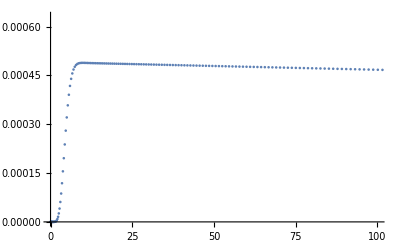

```mathematica
ListPlot[plist,PlotRange->{{0,100},{0,1*10^-3.2}}]
```

```mathematica
gAG [tau_]= Integrate[fTP[t],{t,0.0001,tau}]
```

∫_0.0001^tau InterpolatingFunction[…][t]ⅆt

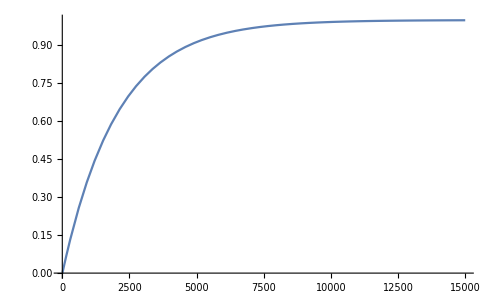

```mathematica
Plot[gAG [tau],{tau,0,15000},PlotRange->All]
```

```mathematica
(* Self antigen *)
```

```mathematica
Xt=10000;
sigma = 15.0
koff =1.0*sigma * scale;
kon = 1.0*scale;
RT=10^4;
LT=1;
nkp=10;
kt=1.0 * scale;
alpha=kt/(kt+koff);
```

15.

```mathematica
(*10-step*)
sol=NDSolve[{x'[t]==-kon*(x[t]^2)+(koff)*(b1[t]+b2[t])+(koff+kt)*b3[t],
b1'[t]==-kt*b1[t]-koff*b1[t]+kon*(x[t]^2),
b2'[t]==-kt*b2[t]-koff*b2[t]+kt*b1[t],
b3'[t]==-kt*b3[t]-koff*b3[t]+kt*b2[t],
b4'[t]==-kt*b4[t]-koff*b4[t]+kt*b3[t],
b5'[t]==-kt*b5[t]-koff*b5[t]+kt*b4[t],
b6'[t]==-kt*b6[t]-koff*b6[t]+kt*b5[t],
b7'[t]==-kt*b7[t]-koff*b7[t]+kt*b6[t],
b8'[t]==-kt*b8[t]-koff*b8[t]+kt*b7[t],
b9'[t]==-kt*b9[t]-koff*b9[t]+kt*b8[t],
b10'[t]==-(kt+koff)*b10[t]+kt*b9[t],
y'[t]==kt*b10[t]*(1-y[t]),x[0]==Xt,b1[0]==0,b2[0]==0,b3[0]==0,b4[0]==0,b5[0]==0,b6[0]==0,b7[0]==0,b8[0]==0,b9[0]==0,b10[0]==0,y[0]==0},{x,y},{t,0,100000000},WorkingPrecision->30];
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==15. (b1[t]+b2[t])+16. b3[t]-1. x[t]^2,b1'[t]==-16. b1[t]+1. x[t]^2,b2'[t]==1. b1[t]-16. b2[t],b3'[t]==1. b2[t]-16. b3[t],b4'[t]==1. b3[t]-16. b4[t],b5'[t]==1. b4[t]-16. b5[t],b6'[t]==1. b5[t]-16. b6[t],b7'[t]==1. b6[t]-16. b7[t],b8'[t]==1. b7[t]-16. b8[t],b9'[t]==1. b8[t]-16. b9[t],«14»},{},{},{},{}}) is less than WorkingPrecision (30.).

```mathematica
(*3-step*)
sol=NDSolve[{x'[t]==-kon*(x[t]^2)+(koff)*(b1[t]+b2[t])+(koff+kt)*b3[t],
b1'[t]==-kt*b1[t]-koff*b1[t]+kon*(x[t]^2),
b2'[t]==-kt*b2[t]-koff*b2[t]+kt*b1[t],
b3'[t]==-(kt+koff)*b3[t]+kt*b2[t],
y'[t]==kt*b3[t]*(1-y[t]),x[0]==Xt,b1[0]==0,b2[0]==0,b3[0]==0,y[0]==0},{x,y},{t,0,100000000},WorkingPrecision->30];
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==5. (b1[t]+b2[t])+6. b3[t]-1. x[t]^2,b1'[t]==-6. b1[t]+1. x[t]^2,b2'[t]==1. b1[t]-6. b2[t],b3'[t]==1. b2[t]-6. b3[t],y'[t]==1. b3[t] (1-y[t]),x[0]==10000,b1[0]==0,b2[0]==0,b3[0]==0,y[0]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

```mathematica
gSELF[t_]=y[t]/.sol
```

{                                                             8
InterpolatingFunction[{{0, 1.00000000000000000000000000000 10 }}, <>][t]}

```mathematica
Function[t,y[t]/.sol]
```

Function[t,y[t]/.sol]

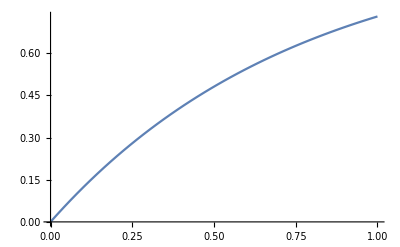

```mathematica
p1=Plot[{gSELF[t]},{t,0,10000000},PlotRange->All]
```

```mathematica
(* TP *)
```

```mathematica
i=0.0001;
k=1;
fixedTParray={};
While[i<N[100000000],
(*ftc[t_]=PDF[ExponentialDistribution[i],t];*)
If[i>15000,fixedTParray=AppendTo[fixedTParray,{i,1}],gamTP=(gSELF[i]+gAG[i] - gSELF[i]*gAG[i]);fixedTParray=AppendTo[fixedTParray,{i,gamTP[[1]]}]];
(*fixedTParray=AppendTo[fixedTParray,{i,gamTP[[1]]}];*)
i=i+1/100+1/100*k;
k=k+1]
```

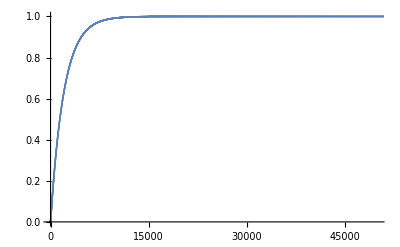

```mathematica
ListPlot[fixedTParray,PlotRange->{{0,50000},{0,1}}]
```

```mathematica
(*FP*)
```

```mathematica
i=0.0001;
k=1;
fixedFParray={};
While[i<N[100000000],
(*ftc[t_]=PDF[ExponentialDistribution[i],t];*)
gamFP=(gSELF[i]);
fixedFParray=AppendTo[fixedFParray,{i,gamFP[[1]]}];
i=i+1/100+1/100*k;
k=k+1]
```

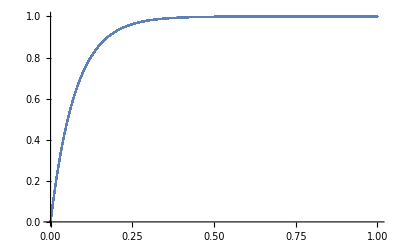

```mathematica
ListPlot[fixedFParray,PlotRange->{{0,100000000},{0,1}}]
```

```mathematica
Length[fixedTParray]
```

141420

```mathematica
Length[fixedFParray]
```

141420

```mathematica
(* Gamma *)
```

```mathematica
Clear[Gam]
```

```mathematica
a=ConstantArray[0,{2,Length[fixedFParray]}];
```

```mathematica
Gam =Transpose[ ConstantArray[0,{2,Length[fixedFParray]}]];
```

```mathematica
Gam[[1]]
```

{0,0}

```mathematica
rhoAG = 0.5;
```

```mathematica
For[i=1,i<=Length[fixedFParray],i=i+1,
Gam[[i,1]]=fixedFParray[[i,1]];
Gam[[i,2]] = (rhoAG) * fixedTParray[[i,2]] + (1-rhoAG)*(1-fixedFParray[[i,2]]) 
]
```

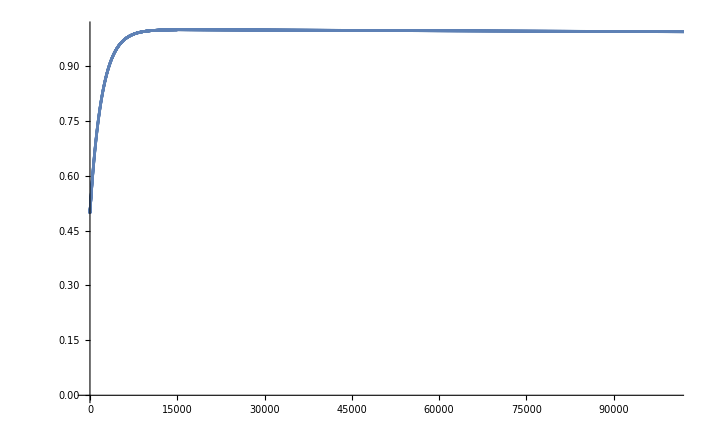

```mathematica
ListPlot[Gam,PlotRange->{{0,100000},{0,1}}]
```

```mathematica
Export["correcctedTDA.h5",Gam,{"Datasets","N10/SIG15/koff1/kt1/kon1/rhoHALF/GAM"},OverwriteTarget->"Append"];
```

```mathematica
(* Finding the tua_star that maximizes Gamma *)
```

```mathematica
Dimensions[Gam]
```

{141420,2}

```mathematica
indMAX = Ordering[Gam[[;;,2]],-1][[1]]
```

1828

```mathematica
tauStar = Gam[[indMAX,;;]][[1]]
```

16717.1

```mathematica
Export["scaled_TDA_comparisons.h5",tauStar,{"Datasets","N10/SIG15/koff1/kt1/kon1/rhoHALF/tau_star_edit"},OverwriteTarget->"Append"];
```

```mathematica
(*Export["FIXED_TIME_TDA.h5",tauStar,{"Datasets","N3/SIG1000/koff1/kt1/kon1/rhoHALF/tau_star"},OverwriteTarget->"Append","AppendMode"->"Overwrite"]*)
```

FIXED_TIME_TDA.h5

```mathematica
Import["scaled_TDA_comparisons.h5","/N10/SIG15/koff10/kt10/kon10/rhoHALF/tau_star"]
```

16717.1

```mathematica
(* Looking at Outcome Statistics relevant to tau_star *)
```

```mathematica
(* Interpolations *)
```

```mathematica
TP=Interpolation[fixedTParray];
FP=Interpolation[fixedFParray];
```

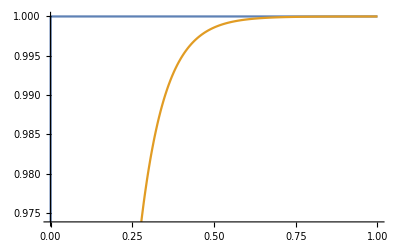

```mathematica
Plot[{TP[t],FP[t]},{t,0,100000000}]
```

```mathematica
(* Generate barplot data of 100*tau_star, 10*tau_star, tau_star, tau_star/10, tau_star/100*)
TPBARS = {TP[100*tauStar],TP[10*tauStar],TP[1*tauStar],TP[0.1*tauStar],TP[0.01*tauStar]}
```

{1.,1.,0.999719,0.558013,0.0765705}

```mathematica
FPBARS = {Min[FP[100*tauStar],1],FP[10*tauStar],FP[1*tauStar],FP[0.1*tauStar],FP[0.01*tauStar]}
```

{0.19704,0.0217059,0.00219202,0.000219353,0.0000218714}

```mathematica
Export["scaled_TDA_comparisons.h5",TPBARS,{"Datasets","N10/SIG15/koff10/kt10/kon10/rhoHALF/TPBARS"},OverwriteTarget->"Append"]
```

scaled_TDA_comparisons.h5

```mathematica
Export["scaled_TDA_comparisons.h5",FPBARS,{"Datasets","N10/SIG15/koff10/kt10/kon10/rhoHALF/FPBARS"},OverwriteTarget->"Append"]
```

scaled_TDA_comparisons.h5